```mathematica
Clear[μ0,ρ]
vA=B0/Sqrt[μ0 ρ]
α[y]=v[y]/vA
Bx[y]=α[y] B0
jp[y]=-D[Bx[y],y]/μ0
```

B0/(√(μ0 ρ))

(√(μ0 ρ) v[y])/B0

√(μ0 ρ) v[y]

-(√(μ0 ρ) v'[y])/μ0

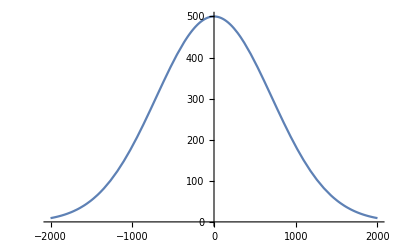

```mathematica
V[y_]:=1000Tanh[y/100]
V[y_]:=500Exp[-y^2/1000^2]
Plot[V[y],{y,-2000,2000}]
```

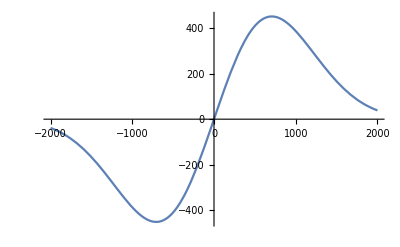

```mathematica
ρ=1.4 10^-12;
μ0=1.257 10^-6;
fac[y_]:=(-√(ρ/μ0)D[V[yp],yp])/.yp->y
Plot[10^6 fac[y],{y,-2000,2000}]
```

```mathematica
Import["D:\\Files\\Research\\Thesis\\Proposal\\SW_EXPT_EFIC_TCT02_20140422T000000_20140422T235959_0302.cdf"]
```

{Timestamp,Latitude,Longitude,Radius,QDLatitude,MLT,Vixh,Vixh_error,Vixv,Vixv_error,Viy,Viy_error,Viz,Viz_error,VsatN,VsatE,VsatC,Ehx,Ehy,Ehz,Evx,Evy,Evz,Bx,By,Bz,Vicrx,Vicry,Vicrz,Quality_flags,Calibration_flags}

```mathematica
dataRaw=Import["D:\\Files\\Research\\Thesis\\Proposal\\SW_EXPT_EFIC_TCT02_20140422T000000_20140422T235959_0302.cdf",{"Datasets",#}]&/@{"Timestamp","Latitude","Radius","VsatN","By","Viy"};
```

```mathematica
data=(Transpose[dataRaw][[2(8 3600+44 60);;2(8 3600+49 60)]])/.{t_List,l_,r_,vs_,b_,v_}->{DateObject[t],l,r,vs,b,v};
```

```mathematica
facBy=10^6 10^-9 2Differences[data[[;;,5]]]/data[[;;-2,4]]/μ0;
```

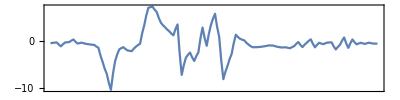

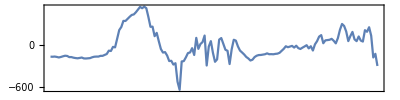

```mathematica
DateListPlot[Transpose[{data[[153;;310,1]],facBy[[153;;310]]}],AspectRatio->1/4,ImageSize->Full,PlotRange->All]
DateListPlot[data[[153;;310,{1,6}]],AspectRatio->1/4,ImageSize->Full]
```

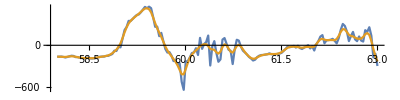

```mathematica
ListLinePlot[{data[[153;;310,{2,6}]],Transpose[{data[[153;;310,2]],GaussianFilter[data[[153;;310,6]],3]}]},AspectRatio->1/4,ImageSize->Full]
```

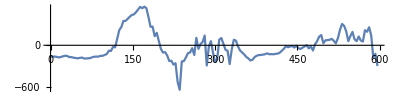

```mathematica
distance=data[[;;,3]]data[[;;,2]]π/180-data[[153,3]]data[[153,2]]π/180;ListLinePlot[Transpose[{distance/1000,data[[;;,6]]}][[153;;310]],AspectRatio->1/4,ImageSize->Full]
```

```mathematica
vel=Transpose[{distance[[153;;310]],GaussianFilter[data[[153;;310,6]],3]}];
dvdy=#2/#1&@@@Transpose[Differences/@Transpose[vel]];
```

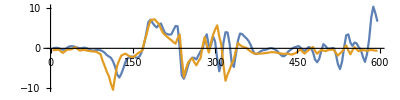

```mathematica
ListLinePlot[{Transpose[{vel[[2;;,1]]/1000,-√(ρ/(10μ0))dvdy 10^6}],Transpose[{vel[[2;;,1]]/1000,facBy[[153;;310-1]]}]},AspectRatio->1/4,ImageSize->Full,PlotRange->All]
```

```mathematica
Import["D:\\Files\\Research\\Thesis\\Proposal\\20150201_35860.000000.h5"]
```

{/J1all,/J2all,/J3all,/Phiall,/Tsall,/nsall,/time/UThour,/time/ymd,/v2avgall,/v3avgall,/vs1all}

```mathematica
x3=Import["D:\\Files\\Research\\Thesis\\test_run\\simgrid.h5",{"Datasets","x3"}][[3;;-3]];
Qp=Import["D:\\Files\\Research\\Thesis\\Proposal\\20150201_36140.000000.h5",{"Datasets","Qp"}];
E0p=Import["D:\\Files\\Research\\Thesis\\Proposal\\20150201_36140.000000.h5",{"Datasets","E0p"}];
fac=Import["D:\\Files\\Research\\Thesis\\Proposal\\20150201_36130.000000.h5",{"Datasets","Vmaxx1it"}];
J1=Import["D:\\Files\\Research\\Thesis\\Proposal\\20150201_35860.000000.h5",{"Datasets","J1all"}];
J2=Import["D:\\Files\\Research\\Thesis\\Proposal\\20150201_35860.000000.h5",{"Datasets","J2all"}];
J3=Import["D:\\Files\\Research\\Thesis\\Proposal\\20150201_35860.000000.h5",{"Datasets","J3all"}];
Ts=Import["D:\\Files\\Research\\Thesis\\Proposal\\20150201_35860.000000.h5",{"Datasets","Tsall"}];
v2=Import["D:\\Files\\Research\\Thesis\\Proposal\\20150201_35860.000000.h5",{"Datasets","v2avgall"}];
ne=Import["D:\\Files\\Research\\Thesis\\Proposal\\20150201_36130.000000.h5",{"Datasets","nsall"}];
```

Import::general: No dataset associated with name nsall

Import::noelem: The Import element "nsall" is not present when importing as HDF5.

```mathematica
{Max[#] 10^6,Position[#,Max[#]]}&/@{J1,J2,J3}
Dimensions@J1
```

{{200.102,{{180,144,1}}},{83.488,{{193,2,14}}},{110.003,{{182,144,12}}}}

{216,144,165}

```mathematica
x2p=181;
x3p=30;
x1p=30;
```

```mathematica
fac//Max
```

9.99909×10^-7

```mathematica
dataIn=Transpose[{x3,#[[;;,x3p]]}]&/@{Qp/Max[Qp],E0p/Max[E0p],fac/Max[fac]};
```

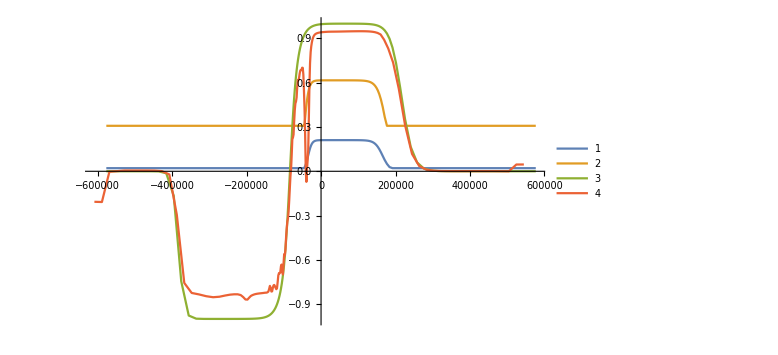

```mathematica
ListLinePlot[Join[dataIn,{Transpose[{x3-32000,J1[[;;,x3p,x1p]] 10^6}]}],ImageSize->Large,PlotLegends->Automatic]
```

```mathematica
fac//Dimensions
```

{}

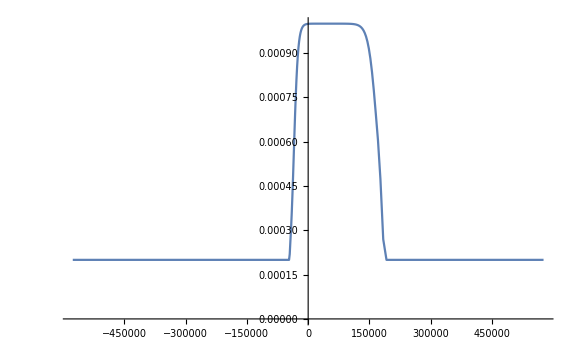

```mathematica
ListLinePlot[Transpose[{x3,Qp[[;;,30]]/E0p[[;;,30]]}],ImageSize->Large,PlotLegends->Automatic]
```

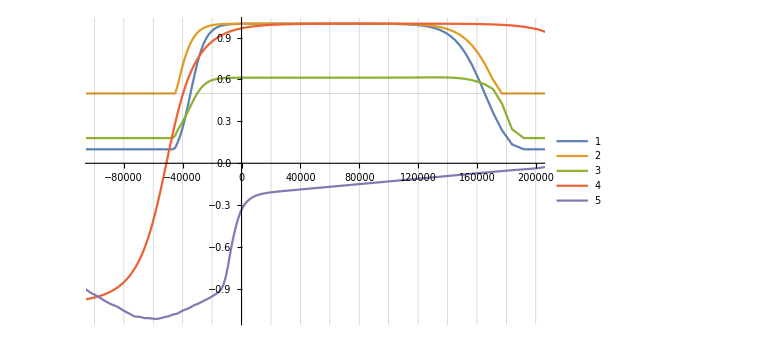

```mathematica
ListLinePlot[Transpose[{x3,#}]&/@{Qp[[;;,30]]/3,E0p[[;;,30]]/3000,ϕ[[;;,30]] 10^7,J1[[;;,30,-1]] 10^6,v2[[;;,30,-1]]/6000},PlotRange->{{-100000,200000},All},ImageSize->Large,PlotLegends->Automatic,GridLines->{All,{0.5}}]
```

```mathematica
e=3000;
ϕ=Qp/(2 E0p^3)e Exp[-e/E0p];
```

```mathematica
ϕ//Max
```

1.01549×10^-7

```mathematica
ListDensityPlot[ϕ]
```

-Graphics-

-Graphics-

```mathematica
ListDensityPlot3D[J1[[100;;,;;,;;50]] 10^6,PlotRange->{-10,10}]
```

-Graphics3D-

```mathematica
gif=Table[Show[ListDensityPlot[J1[[20;;,;;,t]] 10^6,PlotRange->All,PlotLegends->Automatic,ImageSize->Large,AspectRatio->1/2,ColorFunction->"ThermometerColors",PlotLabel->"Height index: "<>ToString[t]],ListContourPlot[Qp,Contours->1,ContourShading->None],ListContourPlot[E0p,ContourStyle->Red,Contours->1,ContourShading->None],ListContourPlot[fac,ContourStyle->Blue,Contours->1,ContourShading->None]],{t,161,1,-5}];
```

```mathematica
Ts//Dimensions
```

{7,216,144,165}

```mathematica
Do[gif0=Table[Show[ListDensityPlot[Ts[[i,20;;,;;,t]] 10^6,PlotRange->All,PlotLegends->Automatic,ImageSize->Large,AspectRatio->1/2,ColorFunction->"ThermometerColors",PlotLabel->"Height index: "<>ToString[t]],ListContourPlot[Qp,Contours->1,ContourShading->None],ListContourPlot[E0p,ContourStyle->Red,Contours->1,ContourShading->None],ListContourPlot[fac,ContourStyle->Blue,Contours->1,ContourShading->None]],{t,161,1,-5}];
Export[NotebookDirectory[]<>"crashT"<>ToString[i]<>"all.gif",gif0,AnimationRepetitions->Infinity,AnimationRate->1/5],{i,2,7,1}]
```

```mathematica
Export[NotebookDirectory[]<>"crash.gif",gif,AnimationRepetitions->Infinity,AnimationRate->1/5]
```

D:\Files\Research\Thesis\Proposal\crash.gif

```mathematica
Show[ListDensityPlot[J1[[20;;,;;,-1]] 10^6,PlotRange->All,PlotLegends->Automatic,ImageSize->Large,AspectRatio->1/2,ColorFunction->"ThermometerColors"],ListContourPlot[fac,Contours->3,ContourShading->None],ListContourPlot[E0p,ContourStyle->Red,Contours->1,ContourShading->None]]
```

-Graphics-

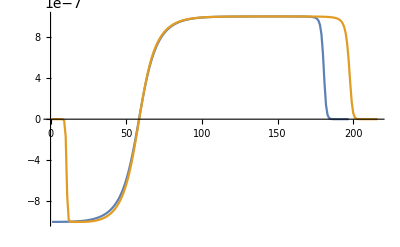

```mathematica
ListLinePlot[{J1[[20;;,30,-1]],fac[[;;,30]]}]
```

```mathematica
Max/@Ts
```

{217343.,209536.,137868.,172366.,291805.,2.23726×10^6,111154.}

-1

-Graphics-

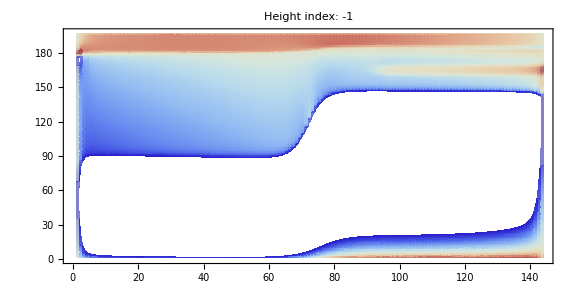

```mathematica
tt=-1
ListDensityPlot[J1[[20;;,;;,tt]] 10^6,PlotRange->{-1,1},PlotLegends->Automatic,ImageSize->Large,AspectRatio->1/2,ColorFunction->"ThermometerColors",PlotLabel->"Height index: "<>ToString[tt]]
ListDensityPlot[J2[[20;;,;;,tt]] 10^6,PlotRange->{-1,1},PlotLegends->Automatic,ImageSize->Large,AspectRatio->1/2,ColorFunction->"ThermometerColors",PlotLabel->"Height index: "<>ToString[tt]]
ListDensityPlot[J3[[20;;,;;,tt]] 10^6,PlotRange->20{-1,1},PlotLegends->Automatic,ImageSize->Large,AspectRatio->1/2,ColorFunction->"ThermometerColors",PlotLabel->"Height index: "<>ToString[tt]]
ListDensityPlot[v2[[20;;,;;,tt]] 10^-3,PlotRange->2{-1,1},PlotLegends->Automatic,ImageSize->Large,AspectRatio->1/2,ColorFunction->"ThermometerColors",PlotLabel->"Height index: "<>ToString[tt]]
```

```mathematica
Max/@{J1,J2,J3}
```

{0.000200102,0.000083488,0.000110003}

```mathematica
Dimensions@J1
```

{216,144,165}

```mathematica
ListDensityPlot[Transpose@J1[[;;,20,;;]] 10^6,PlotRange->{-1,1},PlotLegends->Automatic,ColorFunction->"ThermometerColors"]
```

-Graphics-

```mathematica
ListDensityPlot[Transpose@Ts[[7,;;,20,;;]],PlotRange->All,PlotLegends->Automatic,ColorFunction->"ThermometerColors"]
```

-Graphics-